# ANOMS ANZ@SFO Data Analysis

This is the real deal

```mathematica
SetDirectory["/Users/brucesawhill/Desktop/ANOMS/SFO ANOMS"]
sfoanomsdays=FileNames[];
Length[sfoanomsdays]
sfoanomsdays[[1]]//FullForm  (* a sample *)
```

/Users/brucesawhill/Desktop/ANOMS/SFO ANOMS

268

"20060201.lt6"

```mathematica
sfoapproach= Import["SFO_Approach.csv", "CSV"]
```

{{CINNY,36-10-54.0000,124-45-36.0000},{PIRAT,37-15-27.5400,122-51-48.0700},{BRINY,37-18-17.1400,122-39-41.9600},{OSI,37-23-32.9980,122-16-52.6780},{MENLO,37-27-49.2700,122-09-13.1700},{HEMAN,37-32-01.8600,122-10-24.0000},{DUYET,37-34-02.6400,122-15-10.5400},{NEPIC,37-35-09.2200,122-17-48.7800}}

```mathematica
waypointtabledecimal = Table[{sfoapproach[[i,1]], 
convertdegminsectodecimal[sfoapproach[[i,2]]],
convertdegminsectodecimal[sfoapproach[[i,3]]]},{i,8}]
```

{{CINNY,36.1817,124.76},{PIRAT,37.2577,122.863},{BRINY,37.3048,122.662},{OSI,37.3925,122.281},{MENLO,37.4637,122.154},{HEMAN,37.5339,122.173},{DUYET,37.5674,122.253},{NEPIC,37.5859,122.297}}

```mathematica
sfoairport = {37.6189, 122.3750}  (* Lat Long of SFO *)
```

{37.6189,122.375}

```mathematica
waypointtabledist = Table[{waypointtabledecimal[[i,1]], 
longdistconvert[sfoairport[[2]],waypointtabledecimal[[i,3]],sfoairport[[1]]]-12994,
latdistconvert[sfoairport[[1]],waypointtabledecimal[[i,2]]]-9545},{i,8}]
```

{{CINNY,-222914.,-169250.},{PIRAT,-55977.3,-49687.1},{BRINY,-38224.5,-44452.1},{OSI,-4746.77,-34702.6},{MENLO,6487.8,-26792.4},{HEMAN,4756.07,-18995.8},{DUYET,-2249.59,-15267.7},{NEPIC,-6118.42,-13212.6}}

```mathematica
Export["waypoints.xls", waypointtabledist];
```

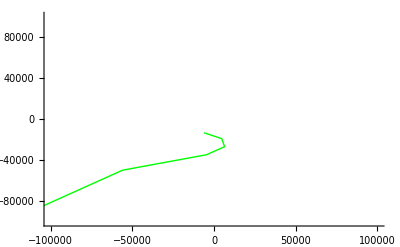

```mathematica
approach=ListPlot[Table[Take[waypointtabledist[[i]],-2],{i,1,8}],PlotRange->{{-100000,100000},{-100000,100000}},Joined->True,PlotStyle->{Green,Thick}]
```

Accessory Functions

```mathematica
latdistconvert[latref_,lat2_]:=
(lat2-latref) 60 1852.
```

```mathematica
longdistconvert[longref_,long2_, latref_]:=
(longref-long2) Cos[latref Degree] 60 1852.
```

```mathematica
convertdegminsectodecimal[degminsec_]:=
{a=StringPosition[degminsec, "-"];
deg =ToExpression[ StringTake[degminsec, {1, a[[1,1]]-1}]];
min = ToExpression[StringTake[degminsec, {a[[1,1]]+1,a[[2,1]]-1}]];
sec = ToExpression[StringTake[degminsec, {a[[2,1]]+1, -1}]];
decimalform = deg + min/60.+sec/3600.
}[[1]]
```

```mathematica
interpolated[data_]:=
{
offsettime = AbsoluteTime[StringJoin[data[[3,1]],"/",data[[4,1]]]];
ld = Length[data];
totaltime = data[[ld,5]];
newdatatable =Table[{},{totaltime+1}]; (* Make a one-second resolution dataset*)
newdatatable[[1]] = data[[21]];
p = 2;(* Set interpolating index *)

Do[
diff = data[[i+1,5]]-data[[i,5]];
Do[
{
newdatatable[[p]]=(diff-j)/diff data[[i]]+j/diff data[[i+1]]; (* Interpolate *)
p++
}
,{j, 1, diff}
]
,{ i, 21,ld-1}
]
Do[newdatatable[[k,5]]=newdatatable[[k,5]]+offsettime, {k, totaltime+1}];
newdatatable
}
```

This plots the location of the aircraft when making a video

```mathematica
acpointplot[proxdata_,pingindex_] := 
 Show[DeleteCases[Table[If[Length[proxdata[[i,pingindex]]]==2, ListPlot[{proxdata[[i,pingindex]]}, 
   PlotRange -> {{-100000, 100000}, {-100000, 100000}}, 
   PlotStyle -> {PointSize[1/20], Opacity[0.2], If[i==1,Red,Blue]}]],{i,Length[proxdata]}],Null]]
```

This plots the contrail leading up to the aircraft when making a video

```mathematica
contrailplot[proxdata_,pingindex_]:=
{
contrails =Table[{},{Length[proxdata]}];
 
Do[contrails[[i]] = 
Table[
If[
Length[proxdata[[i,j]]]≠2, Null,proxdata[[i,j]]
],{j,1,pingindex}
],{i,Length[proxdata]}
];

For[i = 1,i <= Length[contrails], i++, 
{
If[contrails[[i,-1]]==Null , contrails[[i]]=={{}}];
DeleteCases[contrails[[i]],Null]
}
];

DeleteCases[contrails, {{}}];

Show[
Table[
ListPlot[
contrails[[i]],PlotRange->{{-100000,100000},{-100000,100000}},Joined->True
], {i, Length[contrails]}
]
]
}[[1]]
```

This finds a candidate track for interference with a given flight

```mathematica
trackcandidate[flightrecord_]:=
If[flightrecord[[12,1]] =="A",
If[flightrecord[[13,1]]=="SFO",
If[flightrecord[[15,1]]=="28R",
True
]
]
]
```

This finds the start of each flight record by searching for the string "TRACK"

```mathematica
recordstartindices[data_]:=
{
rsi={};
ctr=0;

Do[
{
If[
StringQ[data[[i,1]]]==True,
{ (*  First the data element has to be a string *)
If[
StringLength[data[[i,1]]]≥5,(* Of sufficient length *)
 {
If[
StringTake[data[[i,1]],5]=="TRACK", (* Above two If[]'s avoid error messages here *)
{
ctr++,
rsi=Append[rsi,i];
}
]
}
]
}
]
}, {i, Length[data]}
];
rsi
}[[1]]
```

Once tracks have been parsed out, look for tracks that represent ANZ flights.

```mathematica
stringselect[data_, string_, recordstartindices_]:=
{
selections = {};
For[
i=1, i≤ctr,i++,
{
flight = data[[recordstartindices[[i]]+6,1]], (*  Check for airline code of each track *)

If[
StringQ[flight] == True, (*  Sometimes this record is an empty set *)
If[
StringLength[flight]≥3, (*  Or this record is too short *)
If[
StringTake[flight,3]==string, selections = Append[selections,i]  (* Load track numbers of ANZ flights *)
]
]
]
}
];
selections
}[[1]]
```

```mathematica
ss=stringselect[data,"ANZ",rs]
```

{}

{}

{1100,3106}

```mathematica
pickdata[data_,recordstartindices_,flightrecordnumbers_]:=
{output = {};
If[
Length[flightrecordnumbers]≥1, (* If selections are not the empty set *)
Do[
{
newaddition = Take[data, {recordstartindices[[flightrecordnumbers[[i]]]], recordstartindices[[flightrecordnumbers[[i]]+1]]-1}],
Print[newaddition],
AppendTo[output,newaddition]   (* Pick out and add record from data *)
},{i, Length[flightrecordnumbers]}
]
];
output
}
```

Main

The grand loop to go through all of the data file and pick out all of the ANZ (or any other) flights

```mathematica
nzflights = {};
Do[
ss = 0;
rs = 0;
{
data=Import[sfoanomsdays[[j]], "CSV"];
Print[sfoanomsdays[[j]]],
Print["datalength = ", Length[data]],
rs = recordstartindices[data];
ss = stringselect[data, "ANZ",rs];

If[
Length[ss]≥1, (* If selections are not the empty set *)

Do[
{
newaddition = Take[data, {rs[[ss[[i]]]], rs[[ss[[i]]+1]]-1}],
Print["Length[ss] = ",Length[ss]],
AppendTo[nzflights,newaddition]   (* Pick out and add record from data *)
},{i, Length[ss]}
]

];
Print[j],
(*Clear[data]*)
}, {j,27,27}
]//Timing
```

20090710.lt6

datalength = 746540

Length[ss] = 2

Length[ss] = 2

27

{15.4438,Null}

Parse out flights up to 450 seconds before ANZ flight.

```mathematica
nzlandtime = AbsoluteTime[StringJoin[Take[data, {rs[[ss[[1]]]]+2}][[1,1]],"/",Take[data, {rs[[ss[[1]]]]+4}][[1,1]]]]; (* Benchmark time *)
beforeindices = {};
numflightsbefore = 1;
deltat = 0;
While[deltat ≤450, (*Go back in time to find close flights*)
{fr = Take[data,{rs[[ss[[1]]-numflightsbefore]],
rs[[ss[[1]]-numflightsbefore+1]]-1}];
If[
trackcandidate[fr]==True,
{
time = AbsoluteTime[StringJoin[fr[[3,1]],"/",fr[[5,1]]]],
deltat=nzlandtime-time,
AppendTo[beforeindices,ss[[1]]-numflightsbefore],
Print[time]
}
]
};
 numflightsbefore++
]
```

AbsoluteTime::ambig: Warning: the interpretation of the string 07/10/2009/12:23:45 as a date is ambiguous.

AbsoluteTime::ambig: Warning: the interpretation of the string 07/10/2009/12:22:22 as a date is ambiguous.

3456217342

AbsoluteTime::ambig: Warning: the interpretation of the string 07/10/2009/12:19:59 as a date is ambiguous.

3456217199

AbsoluteTime::ambig: Warning: the interpretation of the string 07/10/2009/12:13:03 as a date is ambiguous.

General::stop: Further output of AbsoluteTime will be suppressed during this calculation.

3456216783

Parse flights up to 450 seconds after ANZ flight

```mathematica
nzlandtime = AbsoluteTime[StringJoin[Take[data, {rs[[ss[[1]]]]+2}][[1,1]],"/",Take[data, {rs[[ss[[1]]]]+4}][[1,1]]]]; (* Benchmark time *)
afterindices = {};
numflightsafter = 1;
deltat = 0;
While[deltat ≤450,(*Look forward in time to find close flights*)
{fr = Take[data,{rs[[ss[[1]]+numflightsafter]],
rs[[ss[[1]]+numflightsafter+1]]-1}];
If[
trackcandidate[fr]==True,
{
time = AbsoluteTime[StringJoin[fr[[3,1]],"/",fr[[5,1]]]],
deltat=time-nzlandtime,
AppendTo[afterindices,ss[[1]]+numflightsafter]
}
]
};
 numflightsafter++
]
```

AbsoluteTime::ambig: Warning: the interpretation of the string 07/10/2009/12:23:45 as a date is ambiguous.

AbsoluteTime::ambig: Warning: the interpretation of the string 07/10/2009/12:26:07 as a date is ambiguous.

AbsoluteTime::ambig: Warning: the interpretation of the string 07/10/2009/12:29:18 as a date is ambiguous.

AbsoluteTime::ambig: Warning: the interpretation of the string 07/10/2009/12:34:00 as a date is ambiguous.

General::stop: Further output of AbsoluteTime will be suppressed during this calculation.

```mathematica
afterindices
```

{1363,1377,1394}

```mathematica
indexlist = Join[{ss[[1]]},beforeindices,afterindices]
```

{1351,1345,1338,1313,1363,1377,1394}

```mathematica
locals=Table[interpolated[Take[data,{rs[[indexlist[[i]]]],rs[[indexlist[[i]]+1]]-1}]],{i,Length[indexlist]}];
```

AbsoluteTime::ambig: Warning: the interpretation of the string 07/10/2009/12:07:35 as a date is ambiguous.

AbsoluteTime::ambig: Warning: the interpretation of the string 07/10/2009/12:02:11 as a date is ambiguous.

AbsoluteTime::ambig: Warning: the interpretation of the string 07/10/2009/12:01:46 as a date is ambiguous.

General::stop: Further output of AbsoluteTime will be suppressed during this calculation.

```mathematica
refstarttime = locals[[1,1,1,5]]
refendtime = locals[[1,1,-1,5]]
earliesttime = Min[Table[locals[[i,1,1,5]],{i,Length[locals]}]]
latesttime =  Max[Table[locals[[i,1,-1,5]],{i,Length[locals]}]]
timespread = latesttime-earliesttime
timematrix = Table[0, {j, Length[locals]},{i,timespread+1}];
Dimensions[timematrix]
refstarttime - earliesttime
refendtime-earliesttime
```

3456216455

3456217425

3456215691

3456218040

2349

{7,2350}

764

1734

```mathematica
Do[
{offset= locals[[i,1,1,5]]-earliesttime,
Do[
timematrix[[i,j + offset]]=Take[locals[[i,1,j]],2],
{j, Length[locals[[i,1]]]}
]
},{i,Length[locals]}]
```

```mathematica
trimmedtimematrix = Table[timematrix[[i,j]],{i,Length[locals]},
{j,refstarttime-earliesttime+1,refendtime-earliesttime+1}];
```

```mathematica
Length[trimmedtimematrix[[1]]]
```

971

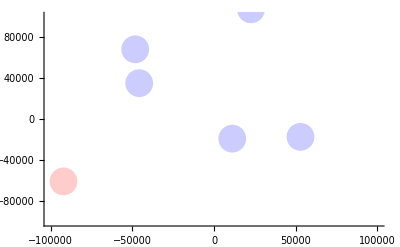

```mathematica
va=acpointplot[trimmedtimematrix,1]
```

```mathematica
vb=contrailplot[trimmedtimematrix,47];
```

```mathematica
Show[va,vb,approach];
```

```mathematica
runway = Point[{-12994,-9545}]
```

Point[{-12994,-9545}]

```mathematica
showrunway = Graphics[{PointSize[.03],Red,runway}];
```

```mathematica
frames = Table[Show[approach, showrunway,acpointplot[trimmedtimematrix,i]],{i,1,Length[trimmedtimematrix[[1]]],3}];
```

```mathematica
Export["sfostargroup1_6.avi", frames];
```

```mathematica
ListAnimate[Table[Show[approach, showrunway,acpointplot[trimmedtimematrix,i]],{i,1,Length[trimmedtimematrix[[1]]],3}]]
```

```mathematica
nzflights=<<nzflights;
```

```mathematica
Length[nzflights]
```

426

```mathematica
filterednzflights=DeleteCases[Table[If[StringMatchQ[nzflights[[i,12]][[1]],"A"]==True && (StringMatchQ[nzflights[[i,15]],"28R"][[1]]==True || 
StringMatchQ[nzflights[[i,15]],"28L"][[1]]==True), nzflights[[i]],0],{i,3, Length[nzflights]}],0];
```

```mathematica
Length[filterednzflights]
```

188

```mathematica
filterednzflights  =<<filterednzflights;
```

```mathematica
Dimensions[filterednzflights]
```

{188}

```mathematica
distance[flight_]:=Sum[flight[[i,4]] (flight[[i+1,5]]-flight[[i,5]]),{i,21, Length[flight]-1}]
```

```mathematica
Length[filterednzflights[[1]]]
```

696

```mathematica
distance[filterednzflights[[1]]]
```

390892

```mathematica
nzdistances = Table[distance[filterednzflights[[i]]],{i,188}];
```

```mathematica
distancefilter[lowerbound_,upperbound_]:=
DeleteCases[Table[If[nzdistances[[i]]≥lowerbound && nzdistances[[i]]<upperbound, i,0],{i,Length[nzdistances]}],0]
```

```mathematica
group1 = distancefilter[120000,145000]
```

{3,4,5,6,7,8,9,10,11,13,14,15,16,17,18,20,21,22,23,24,25,26,27,28,29,30,32,34,35,36,37,40,41,42,43,45,46,47,48,49,51,52,53,54,55,56,57,58,60,61,63,64,66,95,120,131,145,156,164,188}

```mathematica
group1[[16]]
```

20

```mathematica
Take[filterednzflights[[20]],5]
```

{{TRACK 19944585},{8854370},{07/10/2009},{12:07:35},{12:23:45}}

```mathematica
Position[sfoanomsdays,"20090710.lt6"]
```

{{27}}

```mathematica
findricknumber[n_]:-
group1[n]filterednzflights[[4]]
```

```mathematica
group2 = distancefilter[145000,160000]
```

{12,19,31,33,50,65,68,69,70,72,75,77,80,81,83,87,88,91,92,94,96,97,98,102,106,109,111,112,113,116,117,118,122,123,124,125,126,128,129,130,132,133,138,139,140,144,147,152,153,154,157,161,165,166,167,168,169,170,171,172,173,174,178,180,181,184,185,186,187}

```mathematica
group3 = distancefilter[160000,180000]
```

{38,71,73,74,78,82,84,85,86,93,100,101,103,105,108,110,114,115,127,134,135,137,141,142,143,146,148,149,151,160,163,175,176,177,183}

```mathematica
group4 = distancefilter[180000,210000]
```

{2,39,67,76,79,90,99,119,155,158,159,162,182}

```mathematica
Histogram[nzdistances,60, PlotLabel->"Terminal Airspace Track Distance, 188 ANZ7 arrivals", AxesLabel->{"meters", "number"},PlotRange->{{100000,400000},{0,30}}]
```

-Graphics-

Rick groupings  are 120-145km, 145-160km, 160-180km, 180-210km.

```mathematica
universaltime[date_,time_]:=  AbsoluteTime[StringJoin[date,"/",time]];
```

```mathematica
nzdurations = Table[universaltime[filterednzflights[[i,3]],filterednzflights[[i,5]]]-
universaltime[filterednzflights[[i,3]],filterednzflights[[i,4]]],{i,188}]
```

AbsoluteTime::ambig: Warning: the interpretation of the string 07/01/2009/12:09:40 as a date is ambiguous.

AbsoluteTime::ambig: Warning: the interpretation of the string 07/01/2009/11:46:11 as a date is ambiguous.

AbsoluteTime::ambig: Warning: the interpretation of the string 07/02/2009/12:01:11 as a date is ambiguous.

General::stop: Further output of AbsoluteTime will be suppressed during this calculation.

{3141,1756,1086,989,1062,1182,994,1038,1090,947,1086,1409,994,993,1108,998,1012,941,1285,970,934,951,974,938,961,974,998,937,970,1136,1294,966,1274,923,984,1109,1164,1626,1808,1145,990,1143,1121,923,937,1036,993,1048,914,1280,1068,1054,1012,1073,943,946,1043,984,1709,923,942,1828,948,966,1177,1094,1501,1176,1208,1101,1355,1094,1279,1219,1086,1508,1217,1258,1442,1191,1046,1373,1066,1192,1208,1418,1114,1032,2122,1269,1168,1153,1255,1160,982,1161,1138,1355,1489,1291,1212,1057,1239,1933,1365,1123,2455,1360,1156,1404,1150,1097,1116,1148,1199,1115,1178,1112,1408,1071,2614,1169,1167,1218,1110,1161,1284,1150,1190,1213,979,1201,1096,1259,1224,2658,1331,1103,1191,1180,1282,1480,1118,1132,1030,1268,1073,1225,1469,2589,1252,1068,1138,1099,1555,1117,1089,1447,1612,1384,1262,1361,1237,997,1040,1045,1069,1087,1109,1096,1121,1264,1097,1124,1263,1242,1299,1091,2303,1051,1042,1654,1217,1163,1164,1141,1165,1058}

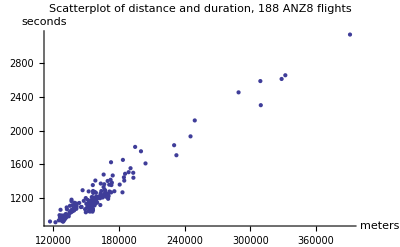

```mathematica
ListPlot[Table[{nzdistances[[i]],nzdurations[[i]]},{i,188}],PlotLabel->"Scatterplot of distance and duration, 188 ANZ8 flights", AxesLabel->{"meters","seconds"}]
```

```mathematica
Histogram[nzdurations,50,PlotRange->{{500,3300},{0,30}},PlotLabel->"Terminal Airspace Residency of ANZ8, 188 Arrivals", AxesLabel->{"sec", "number"}]
```

-Graphics-

```mathematica
Table[filterednzflights[[i,7]],{i,188}]
```

{{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8},{ANZ8}}

```mathematica
correctednzflights=filterednzflights;
```

```mathematica
correctednzflights=Table[If[Abs[filterednzflights[[i,-1,1]]]<1000, 
{filterednzflights[[i,j,1]]-12994,filterednzflights[[i,j,2]]-9545, 
filterednzflights[[i,j,3]],filterednzflights[[i,j,4]],
filterednzflights[[i,j,5]]},filterednzflights[[i,j]]],{i,188},{j,21,Length[filterednzflights[[i]]]}];
```

```mathematica
Table[filterednzflights[[i,-1]],{i,188}]
```

```mathematica
tableofpoints[groupindices_]:=
Table[correctednzflights[[groupindices[[i]]]],{i,Length[groupindices]}];
```

```mathematica
set4=tableofpoints[group4];
```

```mathematica
Export["group4.xls", set4];
```

```mathematica
Length[Flatten[set4,1]]
```

3949

```mathematica
tableofplots[groupindices_]:=Show[Table[ListPlot[Table[{correctednzflights[[groupindices[[i]],j,1]],correctednzflights[[groupindices[[i]],j,2]]},{j,21, Length[correctednzflights[[groupindices[[i]]]]]}]],{i,Length[groupindices]}]]
```

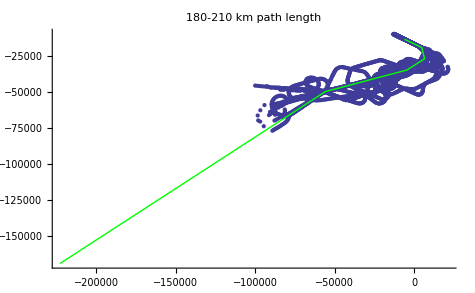

```mathematica
Show[tableofplots[group4],approach,PlotLabel->"180-210 km path length"]
```

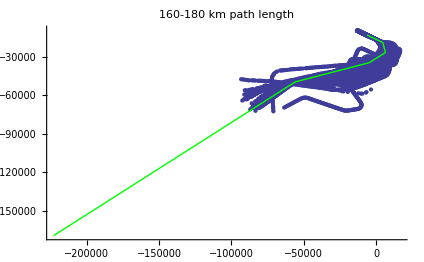

```mathematica
Show[tableofplots[group3],approach,PlotLabel->"160-180 km path length"]
```

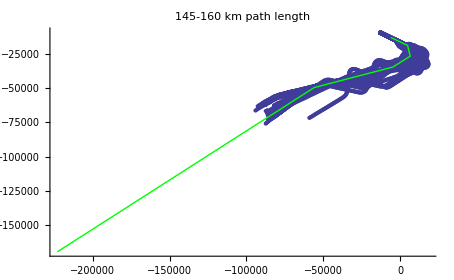

```mathematica
Show[tableofplots[group2],approach,PlotLabel->"145-160 km path length"]
```

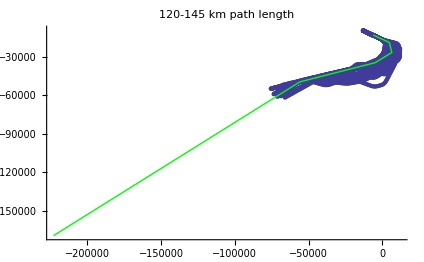

```mathematica
Show[tableofplots[group1],approach,PlotLabel->"120-145 km path length"]
```

```mathematica
tableofplots=Table[ListPlot[Table[{filterednzflights[[i,j,1]],filterednzflights[[i,j,2]]},{j,21, Length[filterednzflights[[i]]]}]],{i,188}];
```

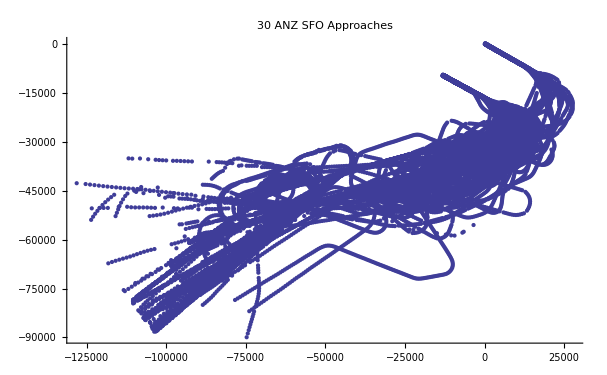

```mathematica
Show[tableofplots, PlotLabel->"30 ANZ SFO Approaches"]
```

```mathematica
nzflights = Take[nzflights, {1, 254}];
```

```mathematica
nzflights>>nzflights;
```

Fills out a dataset to one second intervals

```mathematica
AbsoluteTime[StringJoin[fr[[3,1]],"/",fr[[4,1]]]]
```

3454230533

Previous Analysis

I see it is possible to index a long list of file names because the list is an expression that can be manipulated in a standard way.

Parse the data into individual flights, separate out the trackpoints from the metadata.

```mathematica
trackmatrix=Table[{},{3088}];
startpositioncounter=1;
Do[
{
trackpoints=data[[startpositioncounter+19]][[1]];
trackmatrix[[trackindex]]=Take[data, {startpositioncounter, startpositioncounter+19+trackpoints}];
startpositioncounter=startpositioncounter+20+trackpoints
},{trackindex,  3088}
]
```

A breakout of all of the different kinds of aircraft arriving or departing SFO.

```mathematica
Sort[Tally[DeleteCases[Table[If[trackmatrix[[i,6,1]]=="SFO",trackmatrix[[i,10]],0],{i,3088}],0]], #1[[2]]>#2[[2]]&]
```

{{{J},721},{{R},162},{{T},146},{{B},66},{{H},15},{{P},6},{{U},6},{{M},1}}

Total number of aircraft using SFO

```mathematica
Plus@@Table[If[trackmatrix[[i,6,1]]=="SFO", 1],{i,3088}]
```

1123+1965 Null

Create datamatrix of track data without metadata, normalize time in seconds from 000 hrs Zulu.

```mathematica
datamatrix=Table[Take[trackmatrix[[i]],{21, Length[trackmatrix[[i]]]}], {i,1,3088}];
```

```mathematica
starttimesvector=Table[AbsoluteTime[StringJoin["01 Jan 1900"," ", trackmatrix[[i,4,1]]]],{i,3088}];
Do[
Do[
datamatrix[[i,j,5]]=datamatrix[[i,j,5]]+starttimesvector[[i]],{j,1,Length[datamatrix[[i]]]}
],{i,3088}
];
```

See how many unique seconds are represented.  If everybody is pinged at once, there should be about 1/4 or 1/5 of the seconds in a day.  If aircraft are pinged in sequence, there could be up to the number of seconds in a day, depending on where a particular aircraft is when the radar sweeps by.  The latter hypothesis seems to be true.  Aircraft are pinged by a rotating sweep that is phase distributed.

```mathematica
uniquetimes=Union[Flatten[Table[datamatrix[[i,j,5]],{i,3088},{j,Length[datamatrix[[i]]]}]]];
```

```mathematica
Length[uniquetimes]
```

73983

A filter for finding arrivals at SFO--They start at greater than 3000 meters, traveling faster than 50 m/s, end altitude less than 1000m (not actual runway elevation to allow for data dropouts), and are identified with SFO.

```mathematica
c=0;
indexlist={};
Do[
If[
(
datamatrix[[i,1,3]]≥3000
&&Mean[Table[datamatrix[[i,j,4]], {j,1,10}]]≥50
&&trackmatrix[[i,6,1]]=="SFO"
&&  Take[datamatrix[[i]],-1][[1,3]]<1000
), 
{
c++,
indexlist=Append[indexlist,i]
}], 
{i,3088}
]
Print[c]
```

529

```mathematica
indexlist
```

{30,34,38,48,49,55,65,88,102,109,126,157,159,164,165,172,177,183,189,197,198,201,208,209,216,230,233,238,242,250,254,262,263,266,268,276,281,282,285,291,296,300,304,307,313,314,322,325,329,334,335,341,347,351,357,360,365,366,371,382,388,391,396,402,403,407,411,418,422,426,430,439,440,454,463,466,482,496,502,507,510,516,517,523,524,528,538,539,545,546,557,562,567,571,579,580,585,586,593,597,599,603,604,609,630,639,641,647,651,653,662,678,680,690,692,698,699,708,709,715,717,723,736,740,743,751,754,760,768,773,777,778,783,787,795,800,801,818,820,831,833,836,845,846,848,858,867,868,878,883,888,898,909,919,923,935,940,941,946,952,968,970,974,982,983,988,992,995,1002,1008,1010,1019,1020,1030,1034,1040,1051,1059,1065,1068,1073,1078,1085,1094,1099,1100,1110,1111,1117,1122,1123,1130,1134,1142,1153,1160,1164,1166,1171,1182,1188,1189,1197,1200,1211,1224,1239,1254,1267,1292,1299,1304,1310,1312,1318,1320,1329,1333,1334,1341,1342,1350,1352,1358,1361,1369,1377,1384,1391,1394,1406,1415,1417,1422,1426,1428,1434,1441,1464,1467,1473,1481,1485,1499,1508,1510,1514,1526,1550,1557,1570,1572,1584,1592,1606,1608,1627,1629,1634,1641,1642,1648,1652,1659,1665,1668,1671,1673,1674,1680,1683,1694,1695,1728,1730,1741,1750,1751,1757,1759,1763,1765,1777,1780,1784,1793,1795,1809,1813,1822,1826,1839,1841,1846,1853,1863,1865,1866,1871,1890,1902,1916,1930,1938,1949,1962,1969,1975,1983,1996,2002,2012,2016,2021,2028,2030,2040,2042,2052,2055,2066,2067,2091,2095,2114,2119,2122,2131,2136,2137,2138,2143,2144,2172,2183,2185,2190,2195,2199,2205,2210,2215,2223,2228,2235,2238,2239,2244,2253,2256,2262,2272,2281,2282,2287,2295,2306,2313,2322,2330,2333,2339,2352,2359,2362,2369,2371,2380,2385,2389,2396,2400,2409,2411,2425,2432,2443,2448,2452,2456,2457,2464,2471,2476,2480,2492,2499,2504,2512,2521,2524,2525,2532,2534,2544,2545,2550,2561,2562,2569,2574,2576,2584,2590,2595,2596,2602,2604,2606,2613,2615,2622,2629,2633,2638,2641,2644,2648,2651,2667,2673,2676,2681,2683,2687,2689,2693,2695,2697,2704,2710,2713,2714,2720,2721,2726,2731,2732,2736,2738,2741,2742,2751,2752,2757,2759,2763,2765,2769,2778,2782,2789,2793,2799,2801,2804,2818,2822,2825,2827,2829,2836,2840,2847,2849,2851,2853,2855,2859,2864,2867,2870,2871,2876,2880,2883,2887,2888,2891,2895,2897,2900,2905,2907,2909,2917,2926,2928,2932,2937,2940,2942,2945,2951,2959,2963,2968,2975,2980,2982,2988,2990,2994,2996,2999,3003,3006,3009,3013,3015,3018,3022,3029,3031,3038,3040,3045,3048,3051,3052,3054,3061,3063,3069,3072,3074,3075,3087,3088}

Using trackpoints to determine differentials for speed, acceleration, etc.

```mathematica
difftable[trackmatrixelement_,windowsize_]:=diffs=Table[{Sqrt[(trackmatrixelement[[i+windowsize,1]]-trackmatrixelement[[i,1]])^2+
(trackmatrixelement[[i+windowsize,2]]-trackmatrixelement[[i,2]])^2]//N,trackmatrixelement[[i+windowsize,3]]-trackmatrixelement[[i,3]],trackmatrixelement[[i+windowsize,4]]-trackmatrixelement[[i,4]],
trackmatrixelement[[i+windowsize,5]]-trackmatrixelement[[i,5]]},{i,21,Length[trackmatrixelement]-windowsize}]
```

```mathematica
difftable[trackmatrix[[32]],5];
```

```mathematica
differentials[difftable_]:=differs=Table[{difftable[[i,1]]/difftable[[i,4]],difftable[[i,2]]/difftable[[i,4]],difftable[[i,3]]/difftable[[i,4]]},{i,Length[difftable]}]//N
```

```mathematica
differentials[diffs];
```

```mathematica
differs[[2,1]]
```

206.724

```mathematica
Length[differs]
```

157

```mathematica
trackmatrix[[32,20]]
```

{162}

The data are somewhat noisy

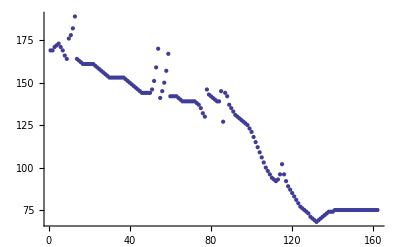

```mathematica
ListPlot[Table[trackmatrix[[35,i,4]],{i,21,182}]]
```

Airspeed is a noisy signal

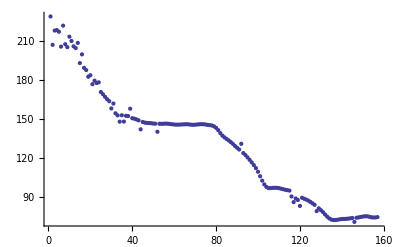

```mathematica
ListPlot[Table[differs[[i,1]],{i,Length[diffs]}]]
```

Definitely an inefficient descent profile

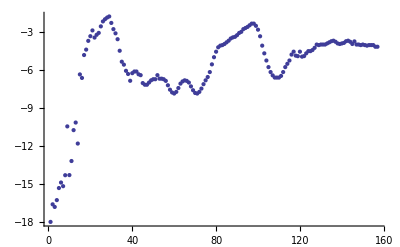

```mathematica
ListPlot[Table[differs[[i,2]],{i,Length[diffs]}]]
```

And a bumpy ride

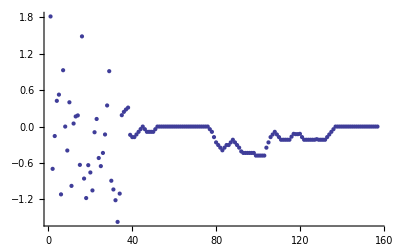

```mathematica
ListPlot[Table[differs[[i,3]],{i,Length[diffs]}]]
```

Create functions for plotting trajectory horizontal and vertical components

```mathematica
planar[index_]:=ListPlot[Table[{trackmatrix[[index,i,1]],trackmatrix[[index,i,2]]},{i,21,Length[trackmatrix[[index]]]}],AxesOrigin->{0,0},AspectRatio->1,PlotJoined->True]
```

```mathematica
vert[index_]:=ListPlot[Table[{Sqrt[(trackmatrix[[index,i,1]]+13000)^2+(trackmatrix[[index,i,2]]+9000)^2],trackmatrix[[index,i,3]]}, {i, 21, Length[trackmatrix[[index]]]}],AxesOrigin->{0,0},PlotJoined->True]
```

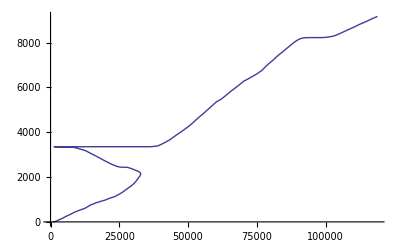

```mathematica
vert[1164]
```

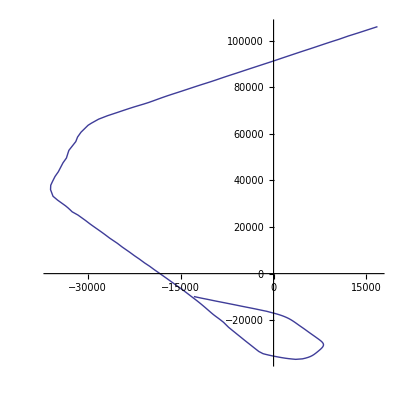

```mathematica
planar[1164]
```

Build a function that detects flat segments of a certain time duration, measured in radar pings (4.2 seconds according to Rick Shay)

```mathematica
flatdetector[dataelement_,numpings_]:=
Table[If[dataelement[[i+numpings,3]]≥dataelement[[i,3]]-25, dataelement[[i,3]],0],{i,Length[dataelement]-10}]
```

This adds the segments to each string of level flying that make up the missed width of the flatdetector[] detection window used to detect the level flying, as the flat elements are only detected after a certain number (6 in the function above, or 25.2 sec) of radar pings.

```mathematica
flatfix[index_,windowsize_]:={
edges={};
workvector=flats[[index]];

Do[
If[
workvector[[i]]≠0 && workvector[[i+1]]==0, 
edges=Append[edges,i]
],{i,1,Length[workvector]-1}
];

Do[
workvector[[edges[[k]]+m]]=datamatrix[[indexlist[[index]],edges[[k]]+m,3]],{k,Length[edges]},{m,windowsize}
];
};
```

```mathematica
flats=Table[flatdetector[datamatrix[[indexlist[[i]]]],6],{i,Length[indexlist]}];
```

```mathematica
levelsegs=flats;
Do[
{
flatfix[i,6],
levelsegs[[i]]=workvector
},{i,529}
]
```

```mathematica
purelevel3=Flatten[Table[DeleteCases[levelsegs[[i]],0], {i, 529}]];
```

```mathematica
Length[purelevel3]
```

15034

Level Flight Fuel Burn Analysis

```mathematica
swa=DeleteCases[Table[If[trackmatrix[[indexlist[[flatties[[i]]]],8,1]]=="SOUTHWEST AIRLINES CO",i,0],{i,74}],0]
```

{15,31,41,47,67}

```mathematica
united=DeleteCases[Table[If[trackmatrix[[indexlist[[flatties[[i]]]],8,1]]=="UNITED AIR LINES INC",i,0],{i,74}],0]
```

{8,10,19,34,35,36,43,55,56}

```mathematica
skywest=DeleteCases[Table[If[trackmatrix[[indexlist[[flatties[[i]]]],8,1]]=="SKY WEST AVIATION INC TRUSTEE",i,0],{i,74}],0]
```

{1,2,3,4,5,6,9,11,13,14,16,18,20,22,26,29,32,33,39,40,42,44,45,46,48,50,58,60,61,62,64,65,68,70,72}

```mathematica
delta=DeleteCases[Table[If[trackmatrix[[indexlist[[flatties[[i]]]],8,1]]=="DELTA AIR LINES INC",i,0],{i,74}],0]
```

{17,37,66,73}

```mathematica
sumsky=0;
Do[
{
trackflats=levelsegs[[flatties[[skywest[[i]]]]]];
sumsky+=Sum[If[trackflats[[j]]>3500, 4.2 crj200fburn[trackflats[[j]]],0],{j,Length[trackflats]}]
},
{i,Length[skywest]}
]
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power will be suppressed during this calculation.

```mathematica
sumsky
```

1131.78

```mathematica
sumsky=0;
Do[
{
trackflats=levelsegs[[flatties[[united[[i]]]]]];
sumsky+=Sum[If[trackflats[[j]]>3500, 4.2 a320fburn[trackflats[[j]]],0],{j,Length[trackflats]}]
},
{i,Length[united]}
]
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power will be suppressed during this calculation.

```mathematica
2.20462 132
```

291.01

```mathematica
sumsky
```

468.564

```mathematica
sumsky=0;
Do[
{
trackflats=levelsegs[[flatties[[delta[[i]]]]]];
sumsky+=Sum[If[trackflats[[j]]>3500, 4.2 a320fburn[trackflats[[j]]],0],{j,Length[trackflats]}]
},
{i,Length[delta]}
]
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power will be suppressed during this calculation.

```mathematica
sumsky
```

131.822

```mathematica
sumsky=0;
Do[
{
trackflats=levelsegs[[flatties[[swa[[i]]]]]];
sumsky+=Sum[If[trackflats[[j]]>3500, 4.2 a320fburn[trackflats[[j]]],0],{j,Length[trackflats]}]
},
{i,Length[swa]}
]
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power will be suppressed during this calculation.

```mathematica
sumsky 2.20462
```

467.737

```mathematica
uniqueaircraftpicker=Table[If[levelsegs[[i,j]]>=3500,i,0],{i,529},{j,Length[levelsegs[[i]]]}];
```

```mathematica
flatties=DeleteCases[Union[Flatten[uniqueaircraftpicker]],0]
```

{10,11,13,17,21,30,34,37,58,64,65,79,97,119,120,132,148,151,154,162,167,178,180,186,187,188,191,196,197,200,202,206,217,221,225,227,230,235,238,244,245,260,262,263,264,265,269,273,277,282,307,311,321,324,340,342,345,348,350,352,358,368,378,379,382,388,407,433,435,474,497,513,515,519}

```mathematica
Length[flatties]
```

74

```mathematica
Tally[Table[trackmatrix[[indexlist[[flatties[[i]]]],8]],{i,Length[flatties]}]]
```

{{{SKY WEST AVIATION INC TRUSTEE},35},{{MESABA AVIATION},2},{{UNITED AIR LINES INC},9},{{VIRGIN AMERICA},2},{{SOUTHWEST AIRLINES CO},5},{{DELTA AIR LINES INC},4},{{KLM ROYAL DUTCH AIRLINES},1},{{DEUTSCHE LUFTHANSA, A.G.},2},{{AIR CHINA},1},{{UNKNOWN},3},{{RELATIONAL INVESTORS LLC},1},{{JAPAN PHOTO HOLDING AS},1},{{CONTINENTAL AIR LINES INC},1},{{EXECUTIVE JET AVIATION INC},2},{{SWISSAIR},1},{{HORIZON AIR INC},1},{{AMERICAN AIRLINES INC},1},{{JETBLUE AIRWAYS CORP},1},{{AMERICA WEST AIRLINES},1}}

```mathematica
Length[Flatten[levelsegs]]
```

103089

```mathematica
1805 4.2/60
```

126.35

```mathematica
16917-(1805 + 8259)
```

6853

```mathematica
126 30 365/60
```

22995

```mathematica
levelsegsflat=Flatten[levelsegs];
```

```mathematica
ctr=0;
Do[If[purelevel3[[i]]>3500, ctr++],{i, Length[purelevel3]}];
ctr
```

1582

```mathematica
1582 4.2/60
```

110.74

```mathematica
Solve[3600 2/x==16.8,x]
```

{{x→428.571}}

```mathematica
ftbins=BinCounts[3.28 purelevel3, {-500, 31500,1000}]
```

{17,29,286,138,1025,619,610,353,1889,183,1497,6806,176,50,348,98,2,209,23,102,175,84,18,27,71,14,36,95,22,13,11,0}

```mathematica
ftbins[[12]]=0
```

0

```mathematica
ftbins[[11]]=0
```

0

```mathematica
ftbins
```

{17,29,286,138,1025,619,610,353,1889,183,0,0,176,50,348,98,2,209,23,102,175,84,18,27,71,14,36,95,22,13,11,0}

```mathematica
BarChart[ftbins,PlotLabel->"Level Flight in Segments>3nm", AxesLabel->{"Altitude (kft)", "Counts (4.2 s)"},ChartLabels->Table[ToString[i], {i,0,32}]]
```

-Graphics-

```mathematica
11500/3.28
```

3506.1

```mathematica
Histogram[Flatten[purelevel3],PlotRange->{0,2000},PlotLabel->"Time Spent in >3 nm Level Flight Segments, SFO Approach", AxesLabel->{"Altitude(m)","Time Counts(4.2 s)"}]
```

-Graphics-

```mathematica
6626 + 1633
```

8259

```mathematica
profile[index_]:={
vert[index],
planar[index]
}
```

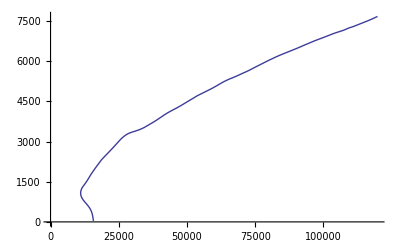
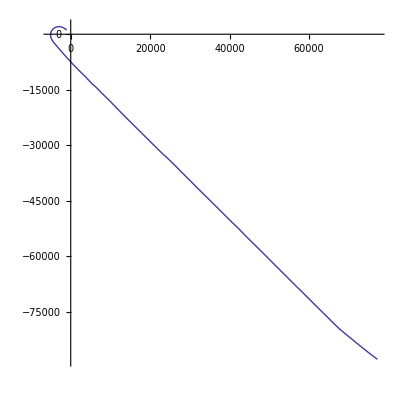

```mathematica
profile[2]
```

```mathematica
Take[trackmatrix[[1]],3]
```

{{TRACK 21895420},{11229198},{05/04/2011}}

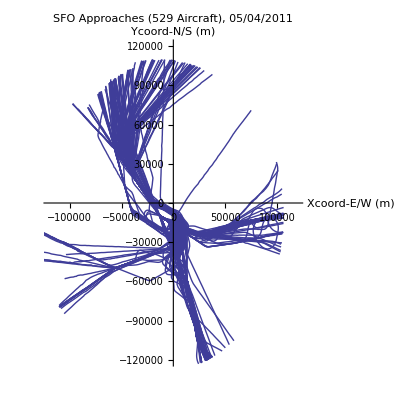

```mathematica
Show[Table[planar[indexlist[[i]]],{i,529}],PlotRange->{{-120000,120000},{-120000,120000}},PlotLabel->"SFO Approaches (529 Aircraft), 05/04/2011",AxesLabel->{ "Xcoord-E/W (m)","Ycoord-N/S (m)"}]
```

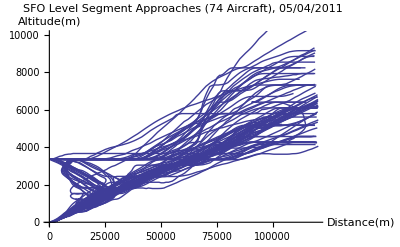

```mathematica
Show[Table[vert[indexlist[[flatties[[i]]]]],{i,1,74}],PlotRange->{{0,120000},{0,10000}},PlotLabel->"SFO Level Segment Approaches (74 Aircraft), 05/04/2011",AxesLabel->{ "Distance(m)","Altitude(m)"}]
```